# 1D

```mathematica
ymap0[f_,n_,x_]:=Integrate[Exp[n f[z]],{z,0,x}]
ymap0[f_,n_,x_]:=Integrate[Exp[n f[z]],{z,0,x}]
```

```mathematica
SeedRandom[7];
yi =RandomReal[{0,1},6];
xi=Table[i/Length[yi],{i,0,Length[yi]}];
```

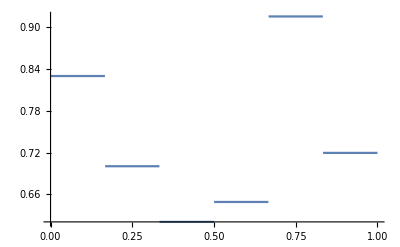

```mathematica
f[x_]=Piecewise[Table[{yi[[i]],xi[[i]]<x<xi[[i+1]]},{i,1,Length[yi]}]];
yf[x_,n_]=Integrate[Exp[n f[z]],{z,0,x},Assumptions->x∈Reals]/Integrate[Exp[n f[z]],{z,0,1}];
yfinv[x_,n_]=InverseFunction[yf,1,2][x,n];
Plot[f[x],{x,0,1}]
```

```mathematica
xrange = Table[i,{i,0,1,0.05}];
With[{n=-50},
Show[Plot[f[x],{x,0,1}],
ListPlot[Table[{x,f[x]-0.01},{x,xrange}],PlotMarkers->"*",PlotStyle->Red],
ListPlot[Table[{yfinv[x,n],f[yfinv[x,n]]+0.01},{x,xrange}],PlotMarkers->"*",PlotStyle->Black]]]
```

-Graphics-

```mathematica
f[x_]:=1/20 x^4-x^2-x+10
y[x_,n_]:=10/Integrate[f[y]^n,{y,-5,5}] Integrate[f[y]^n,{y,-5,x}]-5
```

```mathematica
ClearAll[g, yg]
q=Interpolation[{{0,3},{0.15,1},{0.25,3},{0.75,0.25},{1,5}}];
g[x_]:=q[x]+2
yg[x_?NumericQ,n_]:=1/NIntegrate[Exp[n g[y]],{y,0,1}] NIntegrate[Exp[n g[y]],{y,0,x}]
```

```mathematica
?InverseFunction
```

RowBox[{"InverseFunction", "[", StyleBox["f", "TI"], "]"}] represents the inverse of the function StyleBox["f", "TI"], defined so that RowBox[{RowBox[{"InverseFunction", "[", StyleBox["f", "TI"], "]"}], "[", StyleBox["y", "TI"], "]"}] gives the value of StyleBox["x", "TI"] for which RowBox[{StyleBox["f", "TI"], "[", StyleBox["x", "TI"], "]"}] is equal to StyleBox["y", "TI"]. 
RowBox[{"InverseFunction", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["tot", "TI"]}], "]"}] represents the inverse with respect to the StyleBox[RowBox[{StyleBox["n", "TI"], ""}]]SuperscriptBox["", "th"] argument when there are StyleBox["tot", "TI"] arguments in all.

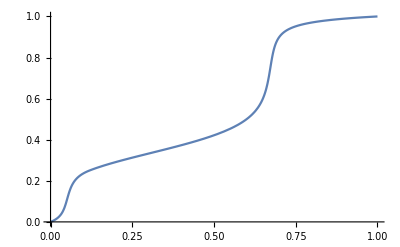

```mathematica
Plot[InverseFunction[yg,1,2][x,1],{x,0,1}]
```

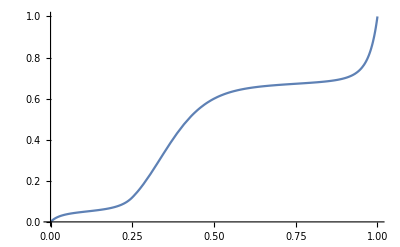

```mathematica
Plot[yg[x,1],{x,0,1}]
```

```mathematica
Show[
Plot[g[x],{x,0,1}],
ListPlot[Table[{x,g[x]},{x,0,1,0.05}],PlotMarkers->"*",PlotStyle->Red]
]
```

-Graphics-

```mathematica
With[{n=3},
Show[
Plot[g[x],{x,0,1}],
ListPlot[Table[{yg[x,n],g[yg[x,n]]},{x,0,1,0.05}],PlotMarkers->"*",PlotStyle->Red]
]]
```

-Graphics-

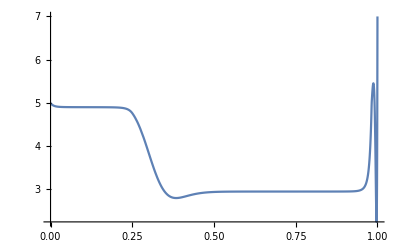

```mathematica
Plot[g[yg[x,3]],{x,0,1}]
```

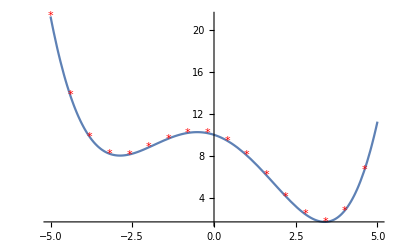

```mathematica
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{x,f[x]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]
```

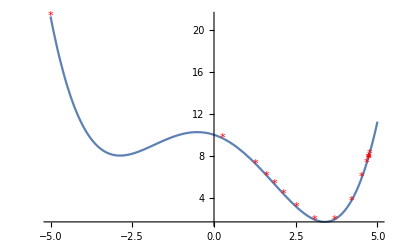

```mathematica
With[{n=4},
Show[
Plot[f[x],{x,-5,5}],
ListPlot[Table[{y[x,n],f[y[x,n]]},{x,-5,5,0.6}],PlotMarkers->"*",PlotStyle->Red]
]]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

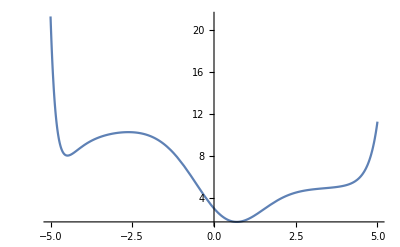

```mathematica
Plot[f[Evaluate@y[x,2]],{x,-5,5}]
```

# 2D

## Piecewise

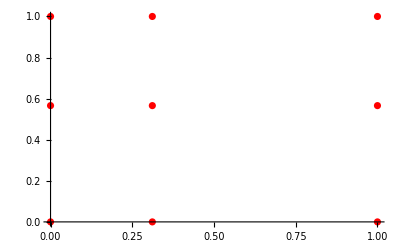

```mathematica
SeedRandom[4];
n=1;
rx={0}~Join~RandomReal[{0,1},n]~Join~{1};
ry={0}~Join~RandomReal[{0,1},n]~Join~{1};
vals = ArrayReshape[RandomReal[{0,1},(n+1)^2],{n+1,n+1}];
grid = ArrayReshape[Table[{rx[[i]],ry[[j]]},{i,1,n+2},{j,1,n+2}]//Flatten,{(n+2)^2,2}];
gridFunc[x_,y_]:=Piecewise[Flatten[Table[{vals[[i,j]],rx[[i]]<x<rx[[i+1]]&&ry[[j]]<y<ry[[j+1]]},{i,1,n+1},{j,1,n+1}],1]]

ListPlot[grid,PlotStyle->{Thick,Red}]
```

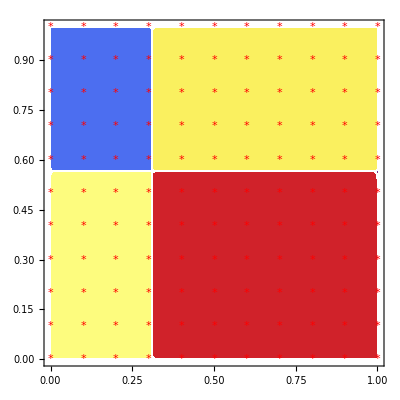

```mathematica
Show[
DensityPlot[Exp[2gridFunc[x,y]],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"],
ListPlot[Table[{x,y},{x,0,1,0.1},{y,0,1,0.1}],PlotMarkers->"*",PlotStyle->Red]
]
```

```mathematica
ξ[λ_,x_,y_]:=Integrate[Exp[-λ gridFunc[xp,y]],{xp,0,x},Assumptions->x∈Reals]
```

```mathematica
ξ[1,x,y]
```

Piecewise[{{0.166309+0.453103 (-0.311376+x), 0.311376<x≤1.&&0.<y<0.566004}, {0.273606+0.519749 (-0.311376+x), 0.311376<x≤1.&&0.566004<y<1.}, {x, x<0.||(y==0.566004&&x>0.)||(y≥1.&&x>0.)||(y≤0.&&x>0.)}, {0.534109 x, 0.<x≤0.311376&&0.<y<0.566004}, {0.878699 x, 0.<x≤0.311376&&0.566004<y<1.}, {-0.521674+x, x>1.&&0.<y<0.566004}, {-0.368482+x, x>1.&&0.566004<y<1.}, {0., True}}]

## 1D recap

```mathematica
n1=5;
SeedRandom[4];
r1 = RandomReal[{-0.5,1.5},n1];

poly1d[x_]:=Product[(x-r1[[i]]),{i,1,n1}]
loss1d[x_]:=10^4 Abs[poly1d[x]]^2+(Abs[x -r1[[1]]]^2)
```

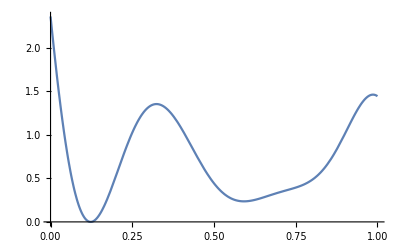

```mathematica
Plot[loss1d[x],{x,0,1}]
```

```mathematica
FindMinimum[loss1d[x],{x,0,1}]
```

{1.13378×10^-17,{x→0.122752}}

```mathematica
ξ[λ_,x_?NumericQ]:=NIntegrate[Exp[-λ loss1d[xp]],{xp,0,x}]
u[λ_,xi_?NumericQ]:=Module[{x},x/.FindRoot[ξ[λ,x]==xi,{x,0,1},Method->"Brent"]]
```

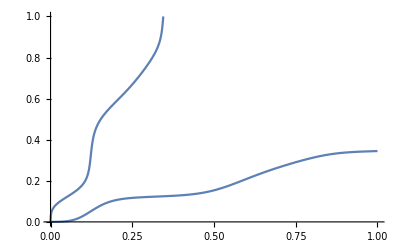

```mathematica
With[{λ=2},Show[Plot[ξ[λ,x],{x,0,1},PlotRange->{{0,1},{0,1}}],Plot[u[λ,xi],{xi,0,ξ[λ,1]},PlotRange->{{0,1},{0,1}}]]]
```

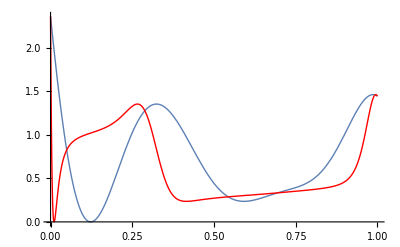

```mathematica
With[{λ=2},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],Plot[loss1d[ξ[λ,x]/ximax],{x,0,1},PlotStyle->{Thick,Red}]]]
```

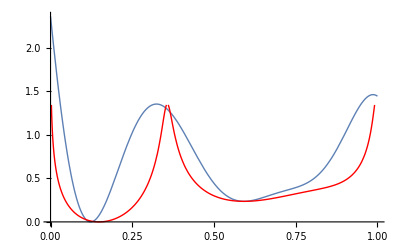

```mathematica
With[{λ=2},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],Plot[loss1d[u[λ,x ximax]],{x,0,1},PlotStyle->{Thick,Red}]]]
```

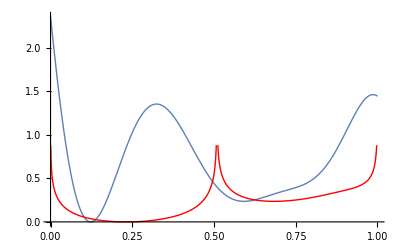

```mathematica
With[{λ=5},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],Plot[loss1d[u[λ,x ximax]],{x,0,1},PlotStyle->{Thick,Red}]]]
```

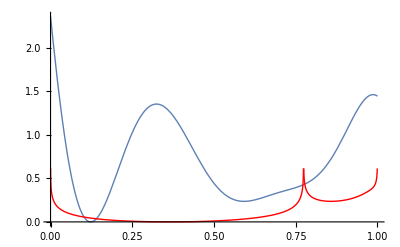

```mathematica
With[{λ=10},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],Plot[loss1d[u[λ,x ximax]],{x,0,1},PlotStyle->{Thick,Red}]]]
```

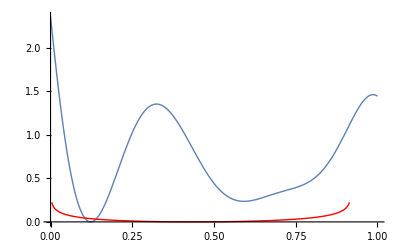

```mathematica
With[{λ=15},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],Plot[loss1d[u[λ,x ximax]],{x,0,1},PlotStyle->{Thick,Red}]]]
```

```mathematica
With[{λ=10},ximax=ξ[λ,1];Table[u[λ,x ximax],{x,{0}}]]
```

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[ξ[10,x$11059651]==0.,{x$11059651,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[ξ[10,x$11059651]==0.,{x$11059651,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ξ[10,x$11059651]==0.,{x$11059651,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x$11059651/.FindRoot[ξ[10,x$11059651]==0.,{x$11059651,0,1},Method→Brent]}

```mathematica
With[{λ=5},ximax=ξ[λ,1];Show[Plot[loss1d[x],{x,0,1},PlotStyle->Thick],ListPlot[Table[{x,loss1d[x]+0.1},{x,0.05,0.95,0.05}],PlotStyle->{Thick,Red},PlotMarkers->"*"],
ListPlot[Table[{u[λ,x ximax],loss1d[u[λ,x ximax]]-0.1},{x,0.05,0.95,0.05}],PlotStyle->{Thick,Black},PlotMarkers->"*"]]]
```

-Graphics-

## Trigonometric

```mathematica
trig2d[a_,b_,c_,d_,x_,y_]:=a Cos[2 π x] Cos[2 π y]+b Cos[2 π y] Sin[2 π x]+c Cos[2 π x] Sin[2 π y]+d Sin[2 π x] Sin[2 π y]
```

```mathematica
Plot3D[trig2d[3,2,0.5,0,x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

## Polynomial

Define a polynomial with random roots. Then define a loss function in such a way that is has global minimum near the first root and local minimums near the other roots.

```mathematica
RandomSeed[5];
n=5;
r1 = RandomReal[{0.2,0.8},n];
r2=RandomReal[{0.2,0.8},n];
r=r1+I r2;

poly2d[z_]:=Product[(z-r[[i]]),{i,1,n}]
loss2d[z_]:=Abs[poly2d[z]]^2+10^(-n-3)(Abs[z -r[[1]]]^2+1)
loss2d[x_,y_]:=loss2d[x+I y]
```

```mathematica
Plot3D[Log[loss2d[x,y]],{x,0,1},{y,0,1}]
```

-Graphics3D-

Standard procedure fails to find the global minimum.

```mathematica
FindMinimum[{10^(n+3)loss2d[x,y],0≤x≤1&&0≤y<=1},{x,y}]
```

{1.27506,{x→0.713993,y→0.744776}}

Choosing good initial point helps.

```mathematica
FindMinimum[{10^(n+3)loss2d[x,y],0≤x≤1&&0≤y<=1},{{x,0.2},{y,0.5}}]
```

{1.,{x→0.217445,y→0.575969}}

Rescale the first variable.

```mathematica
ξ[λ_,x_?NumericQ,y_]:=NIntegrate[Exp[-λ loss2d[xp,y]],{xp,0,x}]
u[λ_,xi_?NumericQ,y_]:=Module[{x},x/.FindRoot[ξ[λ,x,y]==xi,{x,0,1},Method->"Brent"]]
```

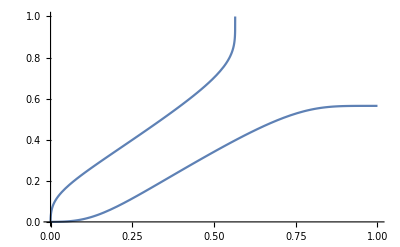

```mathematica
With[{λ=1000,y=0.2},ximax=ξ[λ,1,y];Show[Plot[ξ[λ,x,y],{x,0,1},PlotRange->{{0,1},{0,1}}],Plot[u[λ,xi,y],{xi,0,ximax},PlotRange->{{0,1},{0,1}}]]]
```

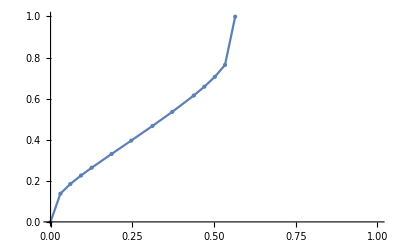

```mathematica
With[{λ=1000,y=0.2},ximax=ξ[λ,1,y];Plot[u[λ,xi,y],{xi,0,ximax},PlotRange->{{0,1},{0,1}},PlotPoints->10,MaxRecursion->1,Mesh->All]]
```

```mathematica
Plot3D[Log[loss2d[x,y]],{x,0,1},{y,0,1},PlotPoints->20,MaxRecursion->1]
```

-Graphics3D-

```mathematica
With[{λ=1000},Plot3D[Log[loss2d[u[λ,x,y],y]],{x,0,1},{y,0,1},PlotPoints->20,MaxRecursion->1]]
```

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[ξ[1000,x$4801020,0.789474]==0.947368,{x$4801020,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[ξ[1000,x$4801020,0.789474]==0.947368,{x$4801020,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ξ[1000,x$4801020,0.789474]==0.947368,{x$4801020,0,1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted